# Mathematica Standalone Example 02

## NSC Ray Trace

A NSC sample file (…\Non-sequential\Miscellaneous\Digital_projector_flys_eye_homogenizer.zmx) is opened, ray trace settings are modified, and then a ray trace is run. Ray trace progress is stored and displayed. After the trace, detector parameters (width, height, number of pixels, etc.) are extracted, as well as pixel data, and detector viewer is recreated and plotted.

## 1. Set up the interface

### Install Mathematica’s NETLink context

```mathematica
Needs["NETLink`"]
```

### Set a default directory and define the path to the ZOS-API libraries

```mathematica
LoadNETType["Microsoft.Win32.Registry"];
zemaxData = Registry`GetValue["HKEY_CURRENT_USER\\Software\\Zemax", "ZemaxRoot", -1];
samplesDir=FileNameJoin[{zemaxData, "\\Samples"}];
```

### Initialize the connection

```mathematica
netHelper = FileNameJoin[{zemaxData, "\\ZOS-API\\Libraries\\ZOSAPI_NetHelper.dll"}];
LoadNETAssembly[netHelper];

LoadNETType["ZOSAPI_NetHelper.ZOSAPI_Initializer"];
success = ZOSAPIUInitializer`Initialize[];
(*Note -- uncomment the following line to use a custom initialization path*)
(*success = ZOSAPIUInitializer`Initialize["C:\\Program Files\\OpticStudio"];*)
```

```mathematica
If[success == True,{
found="Found OpticStudio at: ";
location=ToString[ZOSAPIUInitializer`GetZemaxDirectory[]];
found<>location
}, "Failed to connect!"]
```

{Found OpticStudio at: c:\program files\zemax opticstudio 21.3.1}

### Load assemblies

```mathematica
zosapi=LoadNETAssembly[FileNameJoin[{location, "\\ZOSAPI.dll"}]];
interfaces=LoadNETAssembly[FileNameJoin[{location, "\\ZOSAPI_Interfaces.dll"}]];
```

### Open connection and create the application

```mathematica
(*Open connection and create an application*)
theConnection=NETNew["ZOSAPI.ZOSAPI_Connection"];
theApplication=theConnection@CreateNewApplication[];
```

### Perform final checks regarding the connection

```mathematica
(*Check that a connection was established*)
If[NETObjectQ[theApplication] == False, "An unknown connection error occurred!", "";]
(*Check license status*)
If[theApplication@IsValidLicenseForAPI== False, {
theApplication@CloseApplication[];
"License check failed!"}, ""];
```

## 2. Open a sample file and run a ray trace

### Generate a Mathematica API folder

```mathematica
apiDir=FileNameJoin[{samplesDir, "\\API\\Mathematica"}];
If[DirectoryQ[apiDir]==False, CreateDirectory[apiDir]]
```

### Set up the primary optical system

```mathematica
theSystem = theApplication@PrimarySystem[];
```

```mathematica
(*Open a sample file from the Zemax samples directory*)
testFile = FileNameJoin[{samplesDir,"Non-sequential\\Miscellaneous\\Digital_projector_flys_eye_homogenizer.zmx"}];
theSystem@LoadFile[testFile, False];
```

### Create a ray trace

```mathematica
nscRayTrace = theSystem@Tools@OpenNSCRayTrace[];
```

```mathematica
nscRayTrace@SplitNSCRays = True;
nscRayTrace@ScatterNSCRays = False;
nscRayTrace@UsePolarization = True;
nscRayTrace@IgnoreErrors = True;
nscRayTrace@SaveRays = False;
nscRayTrace@ClearDetectors[0];
```

```mathematica
runRayTrace :=nscRayTrace@RunAndWaitForCompletion[];
runRayTrace;
```

```mathematica
nscRayTrace@Close[];
```

## 3. Analyze the results

### Access the detector results

```mathematica
(*Instead of opening a Detector Viewer, we can pull the detector data straight from the NSCE*)
theNCE = theSystem@NCE;
```

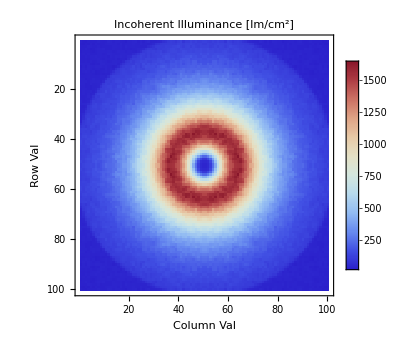

```mathematica
(*Get data for detector 4 with Data = 1*)
data = theNCE@GetAllDetectorDataSafe[4, 1];
ArrayPlot[data, Frame-> True, ColorFunction-> "ThermometerColors", ImageSize-> 350, PlotLabel-> Style["Incoherent Illuminance [lm/cm^2]", 18] , FrameLabel-> {"Row Val","Column Val"}, FrameTicks-> {{True, False},{True, False}}, PlotLegends-> Automatic]
```

```mathematica
ListPlot3D[data, ColorFunction-> "ThermometerColors", ImageSize-> 350, PlotLabel-> Style["Incoherent Illuminance [lm/cm^2]", 18], AxesLabel-> {"Row Val", "Column Val"} ]
```

-Graphics3D-

## Close the application

```mathematica
theApplication@CloseApplication[];
```